```mathematica
S[M_,y_,a_,b_]:=a*b^((2^M-1)*y)+M/((2^M-1)*y)
```

```mathematica
S[M,y,.115,12.54]
```

0.115 12.54^((-1+2^M) y)+M/((-1+2^M) y)

```mathematica
Table[{M,S[M,2^-100,.115,12.54]},{M,90,110}]
```

{{90,92160.1},{91,46592.1},{92,23552.1},{93,11904.1},{94,6016.12},{95,3040.12},{96,1536.13},{97,776.158},{98,392.216},{99,198.407},{100,101.442},{101,68.5839},{102,2869.23},{103,7.03199×10^7},{104,4.2999×10^16},{105,1.60775×10^34},{106,2.24771×10^69},{107,4.39322×10^139},{108,1.67829×10^280},{109,2.44926922503086×10^561},{110,5.21645194494198×10^1123}}

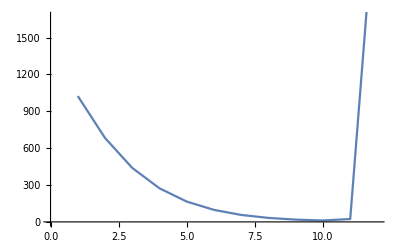

```mathematica
ListPlot[%30,Joined->True]
```

```mathematica
ProbLoadFactor[m_,r_]:=(r/m)^m*(m/r)!/(m/r-m)!
```

```mathematica
ProbN[m_,n_]:=n!/n^n/(n-m)!
```

```mathematica
ProbN[m,m/r]
```

```mathematica
ProbLoadFactor[m,r]
```

((r/m)^m m/r!)/((-m+m/r)!)

```mathematica
Ber[m_,r_]:=r^m(r^-1 m)!/(m^m(m(r^-1-1))!)
```

```mathematica
Simplify[Ber[m,r]-ProbLoadFactor[m,r]]
```

(m^-m (r^m-m^m (r/m)^m) m/r!)/((m (-1+1/r))!)

```mathematica
Ber[m,r]
```

(m^-m r^m m/r!)/((m (-1+1/r))!)

```mathematica
ExpN[m_,r_]:=Sum[(1-ProbLoadFactor[m,r])^(2^n-1),{n,1,1.5*m}]
```

```mathematica
ExpNdr[m_,r_]=D[(1-ProbLoadFactor[m,r])^(2^n-1),r]
```

```mathematica
PartialR[m_,r_]=FullSimplify[(-1+2^n) (1-((r/m)^m (m/r)!)/((-m+m/r)!))^(-2+2^n) (-((r/m)^(-1+m) (m/r)!)/((-m+m/r)!)+(m (r/m)^m Gamma[1+m/r] PolyGamma[0,1+m/r])/(r^2 (-m+m/r)!)-(m (r/m)^m (m/r)! Gamma[1-m+m/r] PolyGamma[0,1-m+m/r])/(r^2 ((-m+m/r)!)^2))]
```

-((-1+2^n) m (r/m)^m Gamma[1+m (-1+1/r)] Gamma[(m+r)/r] (1-((r/m)^m Gamma[(m+r)/r])/Gamma[1+m (-1+1/r)])^(2^n) (r+HarmonicNumber[m (-1+1/r)]-HarmonicNumber[m/r]))/(r^2 ((m (-1+1/r))!-(r/m)^m m/r!)^2)

```mathematica
Sum[PartialR[10,1],{n,1,15}]//N
```

27.7595

```mathematica
PSum[m_,r_]:=Sum[ExpNdr[m,r],{n,1,1.5*m}]
```

```mathematica
PSum[10,.5]//N
```

8.45651

```mathematica
Assuming[q>0&&q<1,Sum[2^n q^(2^n),{n,1,∞}]
```

```mathematica
Sqrt[2*π*m/r]*((m/r)/e)^(m/r)/(m^m*Sqrt[2*π*(m/r-m)]*((m/r-m)/e)^(m/r-m))
```

ⅇ^-m m^-m (-m+m/r)^(-1/2+m-m/r) (m/r)^(1/2+m/r)

```mathematica
Simplify[(m^-m ((-m+m/r)/e)^(m-m/r) √(m/r) (m/(e r))^(m/r))/(√(-m+m/r))]
```

```mathematica
FullSimplify[ⅇ^-m m^-m (m (-1+1/r))^(-1/2+m-m/r) (m/r)^(1/2+m/r)]
```

ⅇ^-m m^-m (m (-1+1/r))^(-1/2+m-m/r) (m/r)^(1/2+m/r)

```mathematica
e
```

e

```mathematica
e//N
```

e

```mathematica
Exp[1]
```

ⅇ

```mathematica
e=Exp[1]
```

ⅇ

```mathematica
N!/N^n/(N-m)!
```

```mathematica
fac[k_]=Sqrt[2*π*k]*(k/Exp[1])^k
```

```mathematica
fac[10]//N
```

3.5987×10^6

```mathematica
fac[N]/N^N/fac[N-m]
```

ⅇ^-m √N (-m+N)^(-1/2+m-N)

```mathematica
ⅇ^-m N^(1/2-n+N) (-m+N)^(-1/2+m-N)
```

ⅇ^-m N^(1/2-n+N) (-m+N)^(-1/2+m-N)

```mathematica
N
```

N

```mathematica
N=m/r
```

m/r

```mathematica
ⅇ^-m N^(1/2-n+N) (-m+N)^(-1/2+m-N)
```

```mathematica
rrr[N_,m_]:=ⅇ^-m √N (-m+N)^(-1/2+m-N)
```

```mathematica
rrr[N,m]
```

ⅇ^-m √N (-m+N)^(-1/2+m-N)

```mathematica
rrr[m/r,m]
```

```mathematica
prr[m_,r_]:=Exp[-m] (-m+m/r)^(-1/2+m-m/r) √(m/r)
```

```mathematica
qr[m_,r_]:=1-prr[m,r]
```

```mathematica
qr[m,.75]
```

1-1.1547 0.333333^(-1/2-0.333333 m) ⅇ^-m m^(-0.333333 m)

```mathematica
qr[m,r]
```

1-ⅇ^-m (-m+m/r)^(-1/2+m-m/r) √(m/r)

```mathematica
RRR[m_,r_,n_]:=D[qr[m,r]^(2^n-1),m]
```

```mathematica
RRR[m,r,n]
```

(-1+2^n) (1-ⅇ^-m (-m+m/r)^(-1/2+m-m/r) √(m/r))^(-2+2^n) (ⅇ^-m (-m+m/r)^(-1/2+m-m/r) √(m/r)-(ⅇ^-m (-m+m/r)^(-1/2+m-m/r))/(2 √(m/r) r)-ⅇ^-m (-m+m/r)^(-1/2+m-m/r) √(m/r) (((-1+1/r) (-1/2+m-m/r))/(-m+m/r)+(1-1/r) Log[-m+m/r]))

```mathematica
prr[10,.5]
```

6.42052×10^-15

```mathematica
Sum[qrr[35,.9999999999999],{n,1,55}]-1/Log[2]
```

∂_35 3.49576390824102×10^-31184780+∂_35 1.86969620933672×10^-15592390+∂_35 1.36736835310133×10^-7796195+∂_35 3.69779441806396×10^-3898098+∂_35 1.92296500889478×10^-1949049+∂_35 4.38516249724826×10^-974525+∂_35 6.62205595414892×10^-487263+∂_35 8.1376015922056×10^-243632+∂_35 2.85264817466576×10^-121816+∂_35 1.68897844283197×10^-60908+∂_35 1.29960703529879×10^-30454+∂_35 1.14000308678921×10^-15227+∂_35 3.37639317772862×10^-7614+∂_35 1.83749644474698×10^-3807+∂_35 4.28660290720883×10^-1904+∂_35 2.0704112914472×10^-952+∂_35 1.43889238498699×10^-476+∂_35 1.19954×10^-238+∂_35 1.09523×10^-119+∂_35 3.30943×10^-60+∂_35 1.81918×10^-30+∂_35 1.34877×10^-15+∂_35 3.67256×10^-8+∂_35 0.000191639+∂_35 0.0138434+∂_35 0.117658+∂_35 0.343013+∂_35 0.585673+∂_35 0.765293+∂_35 0.87481+∂_35 0.935313+∂_35 0.967116+∂_35 0.98342+∂_35 0.991676+∂_35 0.995829+∂_35 0.997912+∂_35 0.998956+∂_35 0.999478+∂_35 0.999739+∂_35 0.999869+∂_35 0.999935+∂_35 0.999967+∂_35 0.999984+∂_35 0.999992+∂_35 0.999996+∂_35 0.999998+∂_35 0.999999+∂_35 0.999999+∂_35 1.+∂_35 1.+∂_35 1.+∂_35 1.+∂_35 1.+∂_35 1.+∂_35 1.-1/Log[2]

```mathematica
Sum[fq[20,1],{n,1,100}]
```

100 ∂_20 ComplexInfinity

```mathematica
Clear[m]
```

```mathematica
Clear[n]
```

```mathematica
Pdm[m_,r_]:=Assuming[D[ProbLoadFactor[m,r],m],Element[m,Integers]]
```

```mathematica
FullSimplify[Pdm[m,r]]
```

m∈Integers

```mathematica
ProbN[m,N]
```

(N^-N N!)/((-m+N)!)

```mathematica
deriv2[m_,N_]:=D[(N^-N N!)/((-m+N)!),m]
```

```mathematica
deriv[m_,N_]:=N!/(N-m)!*PolyGamma[0,N-m]
```

```mathematica
deriv2[m,N]
```

(N^-N N! Gamma[1-m+N] PolyGamma[0,1-m+N])/((-m+N)!)^2

```mathematica
deriv2[10,15]//N
```

∂_10. 2.48857×10^-8

```mathematica
Clear[m]
```

```mathematica
Clear[N]
```

```mathematica
1
```

1

```mathematica
ProbN[m,N]
```

(N^-N N!)/((-m+N)!)

```mathematica
p[m_,t_]:=t^-t*Gamma[t+1]/Gamma[t-m+1]
```

```mathematica
p[m,t]
```

(t^-t Gamma[1+t])/Gamma[1-m+t]

```mathematica
dp[m_,t_]:=D[-p[m,t],m]
```

```mathematica
dp[m,t]
```

(t^t Gamma[1+t] PolyGamma[0,1-m+t])/Gamma[1-m+t]

```mathematica
p[m,t]
```

(t^-t Gamma[1+t])/Gamma[1-m+t]

```mathematica
p[10,10]//N
```

0.00036288

```mathematica
10!/10!
```

1

```mathematica
10!/10^10//N
```

```mathematica
1
```

1

```mathematica
FullSimplify[dp[m,t]]
```

(t^t Gamma[1+t] PolyGamma[0,1-m+t])/Gamma[1-m+t]

```mathematica
dp[m,t]
```

```mathematica
(t^t Gamma[1+t] *PolyGamma[0,1-m+t])/Gamma[1-m+t]
```

(t^t Gamma[1+t] PolyGamma[0,1-m+t])/Gamma[1-m+t]

```mathematica
dp[10,10]
```

∂_10 (-567/1562500)

```mathematica
ExpMT[m_,t_]:=dp[m,t]*Sum[(2^n-1)*(1-N[p[m,t],2000])^(2^(n-2)),{n,1,2*m}]
```

```mathematica
ExpMT[30,35]//N
```

9.84556

```mathematica
Gamma[10]
PolyGamma[0,10]//N
```

362880

2.25175

```mathematica
dp[m,t]
```

(t^t Gamma[1+t] PolyGamma[0,1-m+t])/Gamma[1-m+t]

```mathematica
dp[10,10]//N
```

-2.0946×10^16

```mathematica
dp[m,t]
```

(t^-t Gamma[1+t] PolyGamma[0,1-m+t])/Gamma[1-m+t]